# Simple NCR Model

```mathematica
Clear["Global`*"]
```

## Define (very) simple possible model

```mathematica
eqA1 = A1'[t]==-kon*CG1[t]*A1[t]+rs*CG1A1[t]
```

A1'[t]==-kon A1[t] CG1[t]+rs CG1A1[t]

```mathematica
eqA2 = A2[t]==I20-I2[t]
```

A2[t]==I20-I2[t]

```mathematica
eqCG1 = CG1'[t]==-kon*CG1[t]*A1[t]+rs*CG1A1[t]
```

CG1'[t]==-kon A1[t] CG1[t]+rs CG1A1[t]

```mathematica
eqCG2 = CG2'[t]== -kon*CG2[t]*A2[t]+rs*CG2A2[t]
```

CG2'[t]==-kon A2[t] CG2[t]+rs CG2A2[t]

```mathematica
eqCG1A1=CG1A1[t] ==CG10 - CG1[t]
```

CG1A1[t]==CG10-CG1[t]

```mathematica
eqCG2A2=CG2A2[t] ==CG20 - CG2[t]
```

CG2A2[t]==CG20-CG2[t]

```mathematica
eqI2 = I2'[t]== -vb*(CG1[t]+CG2[t])*I2[t] / (Km + S[t] + I2[t])-va*(CG1A1[t]+CG2A2[t])*I2[t] / (Km + S[t] + I2[t])
```

I2'[t]==-(vb (CG1[t]+CG2[t]) I2[t])/(Km+I2[t]+S[t])-(va (CG1A1[t]+CG2A2[t]) I2[t])/(Km+I2[t]+S[t])

```mathematica
eqF = F'[t] == vb*(CG1[t]+CG2[t])*S[t] / (Km + S[t] + I2[t])+va*(CG1A1[t]+CG2A2[t])*S[t] / (Km + S[t] + I2[t])
```

F'[t]==(vb (CG1[t]+CG2[t]) S[t])/(Km+I2[t]+S[t])+(va (CG1A1[t]+CG2A2[t]) S[t])/(Km+I2[t]+S[t])

```mathematica
eqS = S[t] == S0-F[t]
```

S[t]==S0-F[t]

## Specify initial conditions and solve

```mathematica
reactantInputs ={S0->200,CG10->2,CG20->2,I20->10,A10->0.01};
```

```mathematica
reactantInputsNull ={S0->200,CG10->2,CG20->2,I20->10,A10->0};
```

```mathematica
reactionRates={kon->1,rs->0.1,rns->2000,vb->0.001,va->200,Km->2000};
```

```mathematica
eqSys = {eqA1,eqA2,eqCG1,eqCG2,eqCG1A1,eqCG2A2,eqF,eqS,eqI2,A1[0]==A10,A2[0]==0,CG1[0]==CG10,CG2[0]==CG20,CG1A1[0]==0,CG2A2[0]==0,I2[0]==I20,S[0]==S0,F[0]==0}
```

{A1'[t]==-kon A1[t] CG1[t]+rs CG1A1[t],A2[t]==I20-I2[t],CG1'[t]==-kon A1[t] CG1[t]+rs CG1A1[t],CG2'[t]==-kon A2[t] CG2[t]+rs CG2A2[t],CG1A1[t]==CG10-CG1[t],CG2A2[t]==CG20-CG2[t],F'[t]==(vb (CG1[t]+CG2[t]) S[t])/(Km+I2[t]+S[t])+(va (CG1A1[t]+CG2A2[t]) S[t])/(Km+I2[t]+S[t]),S[t]==S0-F[t],I2'[t]==-(vb (CG1[t]+CG2[t]) I2[t])/(Km+I2[t]+S[t])-(va (CG1A1[t]+CG2A2[t]) I2[t])/(Km+I2[t]+S[t]),A1[0]==A10,A2[0]==0,CG1[0]==CG10,CG2[0]==CG20,CG1A1[0]==0,CG2A2[0]==0,I2[0]==I20,S[0]==S0,F[0]==0}

```mathematica
s=NDSolve[eqSys/.reactantInputs /.reactionRates,{F[t],S[t],A2[t],I2[t],A1[t]},{t,0,1000}];
```

```mathematica
sNull=NDSolve[eqSys/.reactantInputsNull /.reactionRates ,{F[t],S[t],A2[t],I2[t],A1[t]},{t,0,1000}];
```

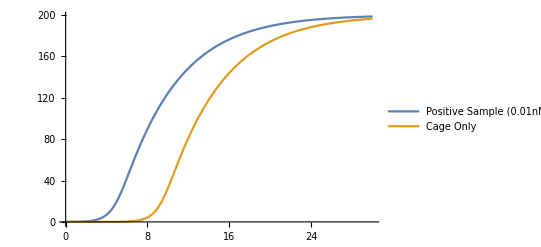

```mathematica
Plot[{Evaluate[F[t]/.s],Evaluate[F[t]/.sNull]},{t,0,30},PlotRange->All,PlotLegends->{"Positive Sample (0.01nM)","Cage Only"}]
```